# Nonclassical energy-change distribution as a witness of non-Markovian quantum dynamics https://arxiv.org/abs/2605.26818

## Definitions (run at the beginning)

Comment: Reusable linear-algebra and quantum-information utilities. Run this chapter once before the figure-specific simulations, since later sections assume these symbols and helper functions are already defined.

### Commonly used matrices

Comment: Defines computational basis vectors, Pauli matrices, ladder operators, and the identity helper Id[n]. These fix the single-qubit notation used throughout the notebook.

```mathematica
m={1,0};p={0,1};
sx = {{0,1},{1,0}};
sy = {{0,-I},{I,0}};
sz = {{1,0},{0,-1}};
id = {{1,0},{0,1}};
sp =(sx - I sy)/2;sm = (sx + I sy)/2;
Id[n_]:=IdentityMatrix[n];
```

### KroneckerProduct, BraKet, DirectSum

Comment: Introduces shorthand operators for tensor products, outer products, direct sums, and pure-state density matrices. These make the later many-body expressions more compact.

```mathematica
CircleTimes[x_?MatrixQ,y_?MatrixQ] := KroneckerProduct[x,y];
CircleTimes[x_?VectorQ,y_?VectorQ] := Flatten[KroneckerProduct[x,y]];
CircleTimes[M_?MatrixQ] := M;
CircleTimes[l_] := CircleTimes@@l;
CircleTimes[a_,b__] := CircleTimes[a, CircleTimes[b]];
```

```mathematica
CircleDot[x_?VectorQ,y_?VectorQ]:= Outer[Times,x,y];
```

```mathematica
CirclePlus[x_?MatrixQ,y_?MatrixQ] := ArrayFlatten[{{x,0},{0,y}}];
CirclePlus[x_?MatrixQ,{}] := x;
CirclePlus[{},y_?MatrixQ] := y;
```

```mathematica
CirclePlus[l_] := CirclePlus@@l;
CirclePlus[a_,b__] := CirclePlus[a, CirclePlus[b]];
```

```mathematica
Todm[v_]:=v⊙Conj[v];
```

### Qubits Systems

Comment: Defines NQubits[NN], which constructs sparse many-qubit spin operators Sx[i], Sy[i], Sz[i], Sp[i], and Sm[i] acting on site i of an NN-qubit register.

```mathematica
NQubits[NN_]:=Module[{σ0,σx,σy,σz,σp,σm,eye,eyeL,eyeR},
σ0 = SparseArray[{{1,0},{0,1}}];
σx = SparseArray[{{0,1},{1,0}}];
σy = SparseArray[{{0,-I},{I,0}}];
σz =SparseArray[{{1,0},{0,-1}}];
σp =(σx - I σy)/2;σm = (σx + I σy)/2;
eye = Id[2^NN];
Do[
eyeL = Id[2^(i-1)];
eyeR = Id[2^(NN-i)];
Sx[i] = SparseArray[CircleTimes[eyeL,σx,eyeR]];
Sy[i] = SparseArray[CircleTimes[eyeL,σy,eyeR]];
Sz[i] = SparseArray[CircleTimes[eyeL,σz,eyeR]];
Sp[i] = SparseArray[CircleTimes[eyeL,σp,eyeR]];
Sm[i] = SparseArray[CircleTimes[eyeL,σm,eyeR]];,{i,1,NN}];];
```

### Reshaping, vectorization and reshuffling

Comment: Defines vectorization, inverse vectorization, row-wise reshaping, and reshuffling maps used to move between states, superoperators, and Choi-matrix representations.

```mathematica
Vec[m_]:=Flatten[Transpose[m]]; 

Unvec[v_List,cols_:0]:=Which[
 (cols== 0)&&IntegerQ[√Length[v]],Transpose[Partition[v,√Length[v]]],
 Mod[Length[v],cols]==0,Transpose[Partition[v,cols]]
];

Res[m_List]:=Flatten[m]; 

Unres[v_List,cols_:0]:=Which[
 (cols== 0)&&IntegerQ[√Length[v]],Partition[v,√Length[v]],
 Mod[Length[v],cols]==0,Partition[v,cols]
];

Reshuffle[ρ_]:=Block[{dim},
	dim = Sqrt[Length[ρ]];
	If[And [SquareMatrixQ[ρ] , IntegerQ[dim]] ,
		Reshuffle[ρ, {{dim,dim},{dim,dim}}]
	(*else*),
		Message[Reshuffle::argerr]
	]
]
Reshuffle::argerr = "Reshuffle works only for square matrices of dimension \!\(\*SuperscriptBox[\"d\", \"2\"]\)×\!\(\*SuperscriptBox[\"d\", \"2\"]\), \
where d is an Integer, for other dimensions use ReshuffleGeneral";

Reshuffle[A_,{n_,m_}]:=Flatten[
	Table[Flatten[Part[A,1+i1;;n[[2]]+i1,1+i2;;m[[2]]+i2]],{i1,0,n[[1]] n[[2]]-1,n[[2]]},{i2,0,m[[1]]*m[[2]]-1,m[[2]]}]
,1];
```

### Partial trace and transposition

Comment: Defines partial trace and partial-transposition utilities for composite Hilbert spaces. Later sections use these routines to extract reduced S, M, and E states and to manipulate bipartitions.

```mathematica
PartialTrace[A_, {}]:=A;
PartialTrace[A_, dim_, {}]:=A;

PartialTrace[A_, s_] := Block[ {d = Length[A], sys},
    If[ IntegerQ[s],
      sys = {s}, (*else*)
      sys = s
    ];  
    If[  IntegerQ[Sqrt[d]],
    If[ Length[sys]==1 ,
      Switch[sys[[1]],
       1, PartialTrace1[A],
       2, PartialTrace2[A],
       _,Print["B1"]; Message[PartialTrace::syserr, sys]
       ], (*else*)
      If[ sys=={1,2} || sys=={2,1},
        Tr[A], (*else*)
        Print["B2"]; Message[PartialTrace::syserr, sys]
      ]
    ]
    ,
    Message[PartialTrace::dimerr, Dimensions[A]]    
    ]
  ];
```

```mathematica
PartialTrace[A_,dim_?VectorQ,s_]:=Block[{sys},
	If[IntegerQ[s], sys={s}, (*else*) sys=s];
    If[Length[dim] == 2 && Length[sys]==1,
	   Switch[sys[[1]],
        1, PartialTrace1[A,dim],
        2, PartialTrace2[A,dim],
        _, Message[PartialTrace::sysspecerr, Length[dim], Select[sys, Or[#>Length[dim],  # < 1]&]]
        ]
        ,(*else*)
        If[Fold[#1 && (1<= #2 <= Length[dim])&,True,sys], 
        	If[Union[sys] == Range[Length[dim]], 
        		Tr[A], (*else*)
                PartialTraceGeneral[A,dim,sys]
        	],
        (*else*)
            Message[PartialTrace::sysspecerr, Length[dim], Select[sys, Or[#>Length[dim],  # < 1]&]]
        ]
    ]
];

PartialTrace::syserr = "The second argument is expected to be 1, 2 or {1,2} (`1` was given)";
PartialTrace::dimerr = "This function expects square matrix of size d^2×d^2 (the matrix of size `1` was given)";
PartialTrace::sysspecerr = "The system specification is invalid. In the case of `1`-partite systems, it is inpossible to trace out with respect to sub-systems `2`.";

PartialTrace1[X_] := Block[{d = Sqrt[Length[X]]}, Total[X[[1 + d # ;; d + d #, 1 + d # ;; d + d # ]] & /@ Range[0, d - 1]]];
PartialTrace2[X_] := Block[{d = Sqrt[Length[X]]}, Total[X[[1 + # ;; d^2 ;; d, 1 + # ;; d^2 ;; d]] & /@ Range[0, d - 1]]];
PartialTrace1[X_, {d1_, d2_}] := Total[X[[1 + d2 # ;; d2 + d2 #, 1 + d2 # ;; d2 + d2 # ]] & /@ Range[0, d1 - 1]];
PartialTrace2[X_, {d1_, d2_}] := Total[X[[1 + # ;; d1*d2 ;; d2, 1 + # ;; d1*d2 ;; d2]] & /@ Range[0, d2 - 1]];

ListReshape[list_, shape_] := 
  FlattenAt[Fold[Partition[#1, #2] &, Flatten[list], Reverse[shape]], 
   1];

PartialTraceGeneral[A_,dim_?VectorQ,sys_?VectorQ] := Block[
	{offset, keep, dispose, keepdim, disposedim, perm1, perm2, perm, tensor},
	offset=Length[dim];
	keep=Complement[Range[offset], sys];
	dispose=Union[sys];
	perm1=Join[dispose,keep];
	perm2=perm1+offset;
	perm=Ordering[Join[perm1,perm2]];
	tensor=ListReshape[A, Join[dim,dim]];
	keepdim=Apply[Times, Join[dim, dim][[keep]]];
	disposedim=Apply[Times, Join[dim, dim][[dispose]]];
	tensor=Transpose[tensor,perm];
	tensor=ListReshape[tensor,{disposedim,keepdim,disposedim,keepdim}];
	Sum[tensor[[i,All,i,All]],{i,1,disposedim}]
];

PartialTranspose[ρ_,dim_?VectorQ,sys_?VectorQ]:=Block[{offset,tensor,perm,idx1,idx2,s,targetsys},
	offset=Length[dim];
	tensor=ListReshape[ρ, Join[dim,dim]];
	targetsys=Union[sys];
	perm=Range[offset*2];
	For[s=1, s<=Length[targetsys], s+=1, 
		idx1 = Position[perm, targetsys[[s]]][[1, 1]];
		idx2 = Position[perm, targetsys[[s]] + offset][[1, 1]];
		{perm[[idx1]],perm[[idx2]]}={perm[[idx2]],perm[[idx1]]};
	];
	tensor=Transpose[tensor,InversePermutation[perm]];
	ListReshape[tensor,Dimensions[ρ]]
];
```

### Von Neumann, Mutual Information

Comment: Collects entropy and information-theoretic utilities, including von Neumann entropy and mutual information. These are used for the LFS-style non-Markovianity diagnostics.

```mathematica
vonNeumann[ρ_,base_:2]:= Module[{eigs,func},
	eigs = Eigenvalues[ρ];
	func[x_]:= If[NumberQ[x]&&Re@x<10^-12,0,-x Log[base,x]];
	Sum[func[eigs[[i]]],{i,1,Length@eigs}]]
```

```mathematica
MutualInformation[ρ_,locdimlist_]:=Module[{ρA,ρB,ρAB,n},
	n= Length@locdimlist;
	ρA = PartialTrace[ρ,locdimlist,{1}];
	ρB = PartialTrace[ρ,locdimlist,{2}];
	Chop[vonNeumann[ρA]+vonNeumann[ρB]-vonNeumann[ρ],10^-12]];
(* When subsystems are qubits *)
MutualInformation[ρ_]:= MutualInformation[ρ,{2,2}]
```

## Figure 1&2

Comment: Baseline simulation block for Figs. 1 and 2. It sets the three-qubit collision model, propagates the trajectory, computes KDQ and RHP witnesses, and generates the corresponding plots.

## PARAMETERS

Comment: Resets model symbols and defines the baseline frequencies, coupling strengths, collision time, inverse temperatures, bath coherence lambda, anisotropy gamma, and initial density matrices.

```mathematica
ClearAll[ω,ωs,ωm,ωe,gsm,gme,γ,λ,ττ,βS,βM,βE]
NN=3;
ω=1.;
ωs=ω;
ωm=ω;
ωe=ω;
gsm=ω/5;
gme=ω/5;
ττ=1/(5ω);
βS=0;
βM=1.;
βE=1.;
λ=0;
γ=0;
```

```mathematica
ρS0=({{1/(1+ⅇ^(βS ωs)), 0}, {0, ⅇ^(βS ωs)/(1+ⅇ^(βS ωs))}});
ρM0=({{1/(1+ⅇ^(βM ωm)), 0}, {0, ⅇ^(βM ωm)/(1+ⅇ^(βM ωm))}});
ρEth=({{1/(1+ⅇ^(βE ωe)), 0}, {0, ⅇ^(βE ωe)/(1+ⅇ^(βE ωe))}});
χE={{0,λ},{λ,0}};
ρE0=ρEth+χE;
```

## COLLISIONS definition and evolution

Comment: Builds local Hamiltonians, the S-M and M-E interaction Hamiltonians, the collision unitaries, the map PhiSME, the full trajectory rhoSME, reduced states, and system-energy increments.

```mathematica
NQubits[NN];
HS=ωs/2 Sz[1];
HM=ωm/2 Sz[2];
HE=ωe/2 Sz[3];
HSM=gsm/2((1-γ)Sx[1].Sx[2]+(1+γ)Sy[1].Sy[2]+Sz[1].Sz[2]);
HME=gme/2((1-γ)Sx[2].Sx[3]+(1+γ)Sy[2].Sy[3]+Sz[2].Sz[3]);
```

```mathematica
USM=MatrixExp[-ⅈ (HS+HM+HE+HSM) ττ];
USMc=MatrixExp[ⅈ (HS+HM+HE+HSM) ττ];
UME=MatrixExp[-ⅈ (HS+HM+HE+HME) ττ];
UMEc=MatrixExp[ⅈ (HS+HM+HE+HME) ττ];
```

```mathematica
ΦSME[σ_]:=(UME.USM.(PartialTrace[σ,{2,2,2},{3}]⊗ρE0).USMc.UMEc)
```

```mathematica
Nsteps=1001;
ρSME={ρS0⊗ρM0⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
ρSM=Chop@PartialTrace[#,{2,2,2},{3}]&/@ρSME;
ρS=Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME;
ρM=Chop@PartialTrace[#,{2,2,2},{1,3}]&/@ρSME;
ρE=Chop@PartialTrace[#,{2,2,2},{1,2}]&/@ρSME;
```

```mathematica
ΔES=Differences[Tr[ωs/2 sz.#]&/@ρS[[1;;]]];
```

## Intermediate Map

Comment: Constructs the reduced dynamical maps and the intermediate map between consecutive time steps, using an operator basis and Choi/superoperator reshaping routines.

```mathematica
GG1={({{1, 0}, {0, 0}}),({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}}),({{0, 0}, {0, 1}})};
```

```mathematica
ΛSelements=Table[
ρSME={op⊗(ρM0)⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME
,{op,GG1}];
```

```mathematica
LS=Chop@Table[Tr[GG1[[k]]†.#]&/@(ΛSelements[[j]]),{k,1,4},{j,1,4}];
LS=Transpose[LS,1<->3];
LS=Transpose[LS,2<->3];
```

```mathematica
R=1/2({{1, 0, 0, 1}, {0, 1, -ⅈ, 0}, {0, 1, ⅈ, 0}, {1, 0, 0, -1}})
```

{{1/2,0,0,1/2},{0,1/2,-ⅈ/2,0},{0,1/2,ⅈ/2,0},{1/2,0,0,-1/2}}

```mathematica
Clear[choi]
choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{p,m}}])&/@LS;
```

```mathematica
(*CHECK THE MAP!*)
(*Chop[LS[[#]].Flatten[ρS[[1]]]-Flatten[ρS[[#]]]]&/@Range[1,Nsteps-1]*)
```

```mathematica
iLS=Inverse[#]&/@LS;
LStl=Chop@Table[LS[[n+1]].iLS[[n]],{n,1,Nsteps-1}];
a=LStl[[1;;,1,1]];
b=LStl[[1;;,1,4]];
c=LStl[[1;;,2,2]];
d=LStl[[1;;,2,3]];
```

```mathematica
(*CHECK THE INTERMEDIATE MAP!*)
(*n=122;
LStl[[n]].Flatten[ρS[[n]]]-Flatten[ρS[[n+1]]]*)
```

## KDQ

Comment: Computes Kirkwood-Dirac quasiprobability terms for the energy-change distribution and extracts the negativity/nonclassicality indicators used as witnesses.

```mathematica
ProjES=#⊙#&/@(Normalize[#]&/@Eigenvectors[sz])
ProjEM=#⊙#&/@(Normalize[#]&/@Eigenvectors[sz])
```

{{{0,0},{0,1}},{{1,0},{0,0}}}

{{{0,0},{0,1}},{{1,0},{0,0}}}

```mathematica
vecKDQΔESarray=Table[Flatten@Table[Tr[ProjES[[j]].Partition[LStl[[n]].Flatten[ProjES[[k]].ρS[[n]]],2]],{j,1,2},{k,1,2}],{n,1,Nsteps-2}];
negqΔESarray=Chop[-1+Total[Abs[#]]]&/@vecKDQΔESarray;
negqΔESarray2=Chop[-1+ρS[[All;;-3,1,1]] (Abs[1-a]+Abs[a])+ρS[[All;;-3,2,2]] (Abs[1-b]+Abs[b])];
```

```mathematica
(*CHECK!*)
(*negqΔESarray[[1;;60]]-negqΔESarray2[[1;;60]]*)
```

## RHP

Comment: Evaluates the RHP-style CP-divisibility witness from the intermediate maps, using Choi-matrix and trace-norm/eigenvalue diagnostics.

```mathematica
Clear[choi]
choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{m,p}}])&/@LStl;
```

```mathematica
g=((Total[Abs[Eigenvalues[#]]]-1)&/@choi[[1;;]]);
(*dg=Chop@Table[g[[n+1]]-g[[n]],{n,1,Nsteps-2}];*)
```

## PLOTS

Comment: Collects the computed diagnostics into plotting arrays and prepares the data used by the figure-specific plotting cells below.

```mathematica
<<"MaTeX`"
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

### FIG.1

Comment: Plot-generation cells for Fig. 1. These cells visualize the time-resolved energy-change signal together with the non-Markovianity witnesses computed above.

```mathematica
font="Times";
LL=100;
p1=ListLinePlot[{
Callout[a-1,Style[MaTeX["a{-}1",Magnification->1.5]],{20,-0.09},{25,-0.075}],Callout[b,Style[MaTeX["b",Magnification->1.5]],Above],Callout[Abs[c]^2(1-(a(1-b))/Abs[c]^2),Style[MaTeX["|c|^2-a(1-b)",Magnification->1.5]],{46,-.1},{30,-0.06}],
Callout[ΔES(*Abs[d]^2(1-(b(1-a))/Abs[d]^2)*),Style[MaTeX["\\langle\Delta E_s\\rangle / \\omega_s",Magnification->1.5]],{60,-0.03},{53,0.005}]},PlotMarkers->{Automatic,10},PlotStyle->{{Darker[Red],Opacity[0.4]},{Darker[Green],Opacity[0.4]},{Darker[Blue],Opacity[0.4]},{Darker[Cyan],Opacity[0.4]}},PlotRange->{{0,LL},All}];

p2=ListLinePlot[{g,negqΔESarray},PlotRange->{{-0.1,LL},{-0.14,0.24}},PlotMarkers->{"OpenMarkers",6},PlotStyle->{{AbsoluteThickness[1.5],Black,Dashing[0.01,0.1-0.01]},{AbsoluteThickness[1.5],Brown,Dashing[0.02,0.1-0.02]},{AbsoluteThickness[1.5],Green,Dashing[0.02,0.1-0.02]}},PlotTheme->"Detailed",PlotLegends->Placed[{Style[MaTeX["g",Magnification->2]],Style[MaTeX["\\mathcal{N}_q",Magnification->2]]},{0.88,0.8}],
Frame->True,
FrameStyle->Directive[FontFamily->font,24,Black],
Axes->False,ImageSize->600,FrameLabel->{"n"},LabelStyle->Directive[FontFamily->font,24,Black]];
```

```mathematica
Show[p2,p1]
```

-Graphics-

```mathematica
font="Times";
LL=100;
p1=ListLinePlot[{
Callout[a-1,Style[MaTeX["a{-}1",Magnification->1.5]],{20,-0.09},{25,-0.075}],Callout[b,Style[MaTeX["b",Magnification->1.5]],Above],Callout[Abs[c]^2(1-(a(1-b))/Abs[c]^2),Style[MaTeX["|c|^2-a(1-b)",Magnification->1.5]],{46,-.1},{30,-0.06}],
Callout[ΔES(*Abs[d]^2(1-(b(1-a))/Abs[d]^2)*),Style[MaTeX["\\langle\Delta E_s\\rangle",Magnification->1.5]],{60,-0.03},{53,0.005}]},PlotMarkers->{Automatic,13},PlotStyle->{{Darker[Red],Opacity[0.4]},{Darker[Green],Opacity[0.4]},{Darker[Blue],Opacity[0.4]},{Darker[Cyan],Opacity[0.4]}},PlotRange->{{0,LL},All}];

p2=ListLinePlot[{g,negqΔESarray},PlotRange->{{-0.1,LL},{-0.14,0.24}},PlotMarkers->{"OpenMarkers",12},PlotStyle->{{AbsoluteThickness[1.5],Black,Dashing[0.01,0.1-0.01]},{AbsoluteThickness[1.5],Brown,Dashing[0.02,0.1-0.02]},{AbsoluteThickness[1.5],Green,Dashing[0.02,0.1-0.02]}},PlotTheme->"Detailed",(*PlotLegends->Placed[{Style[MaTeX["g",Magnification->2]],Style[MaTeX["\\mathcal{N}_q",Magnification->2]]},{0.88,0.8}],*)
Frame->True,
FrameStyle->Directive[FontFamily->font,24,Black],
Axes->False,ImageSize->600,FrameLabel->{"n"},LabelStyle->Directive[FontFamily->font,24,Black]];
Show[p2,(*pa,pb,pc,*)(*pd,*)p1,PlotRange->{{37.6,41.4},{-0.008,0.008}},FrameTicks->{{Automatic,None},{{38,39,40,41,42},None}},ImageSize->400]
```

-Graphics-

```mathematica
Show[p2,(*pa,pb,pc,*)(*pd,*)p1,PlotRange->{{75.6,80.4},{-0.008,0.008}},FrameTicks->{{Automatic,None},{{75,76,77,78,79,80},None}},ImageSize->400]
```

-Graphics-

### FIG.2

Comment: Plot-generation cells for Fig. 2. They reuse the baseline trajectory and diagnostic arrays, but format them for the second figure layout.

```mathematica
P=id⊗({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})⊗id;
```

```mathematica
LSF=Table[MutualInformation[Partition[P.(Id[4]⊗LStl[[n]]).P.Flatten[choi[[n]]],4]]-MutualInformation[choi[[n]]],{n,1,Nsteps-2}];
```

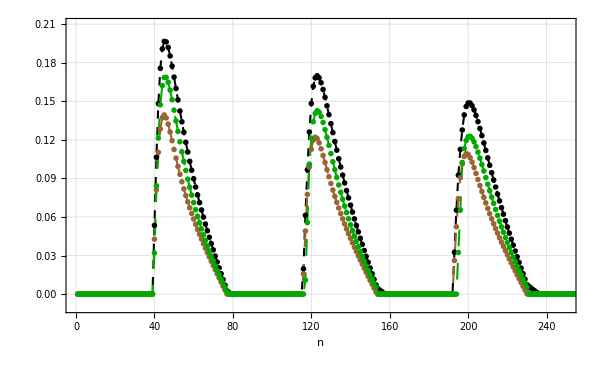

```mathematica
LL=250;
p2=ListLinePlot[{g,negqΔESarray,LSF+(Sign[LSF]-1)/2 LSF},PlotRange->{{-0.1,LL},{-0.01,0.21}},PlotMarkers->{"OpenMarkers",6},PlotStyle->{{AbsoluteThickness[1.5],Black,Dashing[0.01,0.1-0.01]},{AbsoluteThickness[1.5],Brown,Dashing[0.02,0.1-0.02]},{AbsoluteThickness[1.5],Darker[Green],Dashing[0.02,0.1-0.02]}},PlotTheme->"Detailed",PlotLegends->Placed[{Style[MaTeX["g",Magnification->2]],Style[MaTeX["\\mathcal{N}_q",Magnification->2]],Style[MaTeX["\\Delta I_{LS}",Magnification->2]]},{0.65,0.8}],
Frame->True,
FrameStyle->Directive[FontFamily->font,24,Black],
Axes->False,ImageSize->600,FrameLabel->{"n"},LabelStyle->Directive[FontFamily->font,24,Black]]
```

## Figure 3(a)

Comment: Single-run detuned case for Fig. 3(a). The workflow mirrors the baseline block, but with the system frequency shifted relative to the mediator and environment.

## PARAMETERS

Comment: Initializes the same three-qubit collision model as the baseline case, except that omega_s is set to 0.8  to create the detuned run.

```mathematica
ClearAll[ω,ωs,ωm,ωe,gsm,gme,γ,λ,ττ,βS,βM,βE]
NN=3;
ω=1.;
ωs=0.8;
ωm=ω;
ωe=ω;
gsm=ω/5;
gme=ω/5;
ττ=1/(5ω);
βS=0;
βM=1.;
βE=1.;
λ=0;
γ=0;
```

```mathematica
ρS0=({{1/(1+ⅇ^(βS ωs)), 0}, {0, ⅇ^(βS ωs)/(1+ⅇ^(βS ωs))}});
ρM0=({{1/(1+ⅇ^(βM ωm)), 0}, {0, ⅇ^(βM ωm)/(1+ⅇ^(βM ωm))}});
ρEth=({{1/(1+ⅇ^(βE ωe)), 0}, {0, ⅇ^(βE ωe)/(1+ⅇ^(βE ωe))}});
χE={{0,λ},{λ,0}};
ρE0=ρEth+χE;
```

## COLLISIONS definition and evolution

Comment: Builds local Hamiltonians, the S-M and M-E interaction Hamiltonians, the collision unitaries, the map PhiSME, the full trajectory rhoSME, reduced states, and system-energy increments.

```mathematica
NQubits[NN];
HS=ωs/2 Sz[1];
HM=ωm/2 Sz[2];
HE=ωe/2 Sz[3];
HSM=gsm/2((1-γ)Sx[1].Sx[2]+(1+γ)Sy[1].Sy[2]+Sz[1].Sz[2]);
HME=gme/2((1-γ)Sx[2].Sx[3]+(1+γ)Sy[2].Sy[3]+Sz[2].Sz[3]);
```

```mathematica
USM=MatrixExp[-ⅈ (HS+HM+HE+HSM) ττ];
USMc=MatrixExp[ⅈ (HS+HM+HE+HSM) ττ];
UME=MatrixExp[-ⅈ (HS+HM+HE+HME) ττ];
UMEc=MatrixExp[ⅈ (HS+HM+HE+HME) ττ];
```

```mathematica
ΦSME[σ_]:=(UME.USM.(PartialTrace[σ,{2,2,2},{3}]⊗ρE0).USMc.UMEc)
```

```mathematica
Nsteps=1001;
ρSME={ρS0⊗ρM0⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
ρSM=Chop@PartialTrace[#,{2,2,2},{3}]&/@ρSME;
ρS=Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME;
ρM=Chop@PartialTrace[#,{2,2,2},{1,3}]&/@ρSME;
ρE=Chop@PartialTrace[#,{2,2,2},{1,2}]&/@ρSME;
```

```mathematica
ΔES=Differences[Tr[ωs/2 sz.#]&/@ρS[[1;;]]];
```

## Intermediate Map

Comment: Constructs the reduced dynamical maps and the intermediate map between consecutive time steps, using an operator basis and Choi/superoperator reshaping routines.

```mathematica
GG1={({{1, 0}, {0, 0}}),({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}}),({{0, 0}, {0, 1}})};
```

```mathematica
ΛSelements=Table[
ρSME={op⊗(ρM0)⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME
,{op,GG1}];
```

```mathematica
LS=Chop@Table[Tr[GG1[[k]]†.#]&/@(ΛSelements[[j]]),{k,1,4},{j,1,4}];
LS=Transpose[LS,1<->3];
LS=Transpose[LS,2<->3];
```

```mathematica
R=1/2({{1, 0, 0, 1}, {0, 1, -ⅈ, 0}, {0, 1, ⅈ, 0}, {1, 0, 0, -1}})
```

{{1/2,0,0,1/2},{0,1/2,-ⅈ/2,0},{0,1/2,ⅈ/2,0},{1/2,0,0,-1/2}}

```mathematica
Clear[choi]
choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{p,m}}])&/@LS;
```

```mathematica
(*CHECK THE MAP!*)
(*Chop[LS[[#]].Flatten[ρS[[1]]]-Flatten[ρS[[#]]]]&/@Range[1,Nsteps-1]*)
```

```mathematica
iLS=Inverse[#]&/@LS;
LStl=Chop@Table[LS[[n+1]].iLS[[n]],{n,1,Nsteps-1}];
a=LStl[[1;;,1,1]];
b=LStl[[1;;,1,4]];
c=LStl[[1;;,2,2]];
d=LStl[[1;;,2,3]];
```

```mathematica
(*CHECK THE INTERMEDIATE MAP!*)
(*n=122;
LStl[[n]].Flatten[ρS[[n]]]-Flatten[ρS[[n+1]]]*)
```

## KDQ

Comment: Computes Kirkwood-Dirac quasiprobability terms for the energy-change distribution and extracts the negativity/nonclassicality indicators used as witnesses.

```mathematica
ProjES=#⊙#&/@(Normalize[#]&/@Eigenvectors[sz])
ProjEM=#⊙#&/@(Normalize[#]&/@Eigenvectors[sz])
```

{{{0,0},{0,1}},{{1,0},{0,0}}}

{{{0,0},{0,1}},{{1,0},{0,0}}}

```mathematica
vecKDQΔESarray=Table[Flatten@Table[Tr[ProjES[[j]].Partition[LStl[[n]].Flatten[ProjES[[k]].ρS[[n]]],2]],{j,1,2},{k,1,2}],{n,1,Nsteps-2}];
negqΔESarray=Chop[-1+Total[Abs[#]]]&/@vecKDQΔESarray;
negqΔESarray2=Chop[-1+ρS[[All;;-3,1,1]] (Abs[1-a]+Abs[a])+ρS[[All;;-3,2,2]] (Abs[1-b]+Abs[b])];
```

```mathematica
(*CHECK!*)
(*negqΔESarray[[1;;60]]-negqΔESarray2[[1;;60]]*)
```

## RHP

Comment: Evaluates the RHP-style CP-divisibility witness from the intermediate maps, using Choi-matrix and trace-norm/eigenvalue diagnostics.

```mathematica
Clear[choi]
choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{m,p}}])&/@LStl;
```

```mathematica
g=((Total[Abs[Eigenvalues[#]]]-1)&/@choi[[1;;]]);
(*dg=Chop@Table[g[[n+1]]-g[[n]],{n,1,Nsteps-2}];*)
```

## PLOTS

Comment: Collects the computed diagnostics into plotting arrays and prepares the data used by the figure-specific plotting cells below.

```mathematica
<<"MaTeX`"
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

### FIG.3(a)

Comment: Plot-generation cells for Fig. 3(a), using the detuned single-run trajectory and the corresponding witness arrays.

```mathematica
font="Times";
LL=100;
p1=ListLinePlot[{
Callout[a-1,Style[MaTeX["a{-}1",Magnification->1.5]],{78,-0.05},{83,-0.035}],Callout[b,Style[MaTeX["b",Magnification->1.5]],{24,0.025},{22,0.015}],Callout[Abs[c]^2(1-(a(1-b))/Abs[c]^2),Style[MaTeX["|c|^2-a(1-b)",Magnification->1.5]],{70.9,.06},{64,0.039}],
Callout[ΔES/ωs(*Abs[d]^2(1-(b(1-a))/Abs[d]^2)*),Style[MaTeX["\\langle\Delta E_s\\rangle/\omega_s",Magnification->1.5]],{48,-0.03},{53,0.005}]},PlotMarkers->{Automatic,10},PlotStyle->{{Darker[Red],Opacity[0.4]},{Darker[Green],Opacity[0.4]},{Darker[Blue],Opacity[0.4]},{Darker[Cyan],Opacity[0.4]}},PlotRange->{{0,LL},All}];
p2=ListLinePlot[{g,negqΔESarray},PlotRange->{{-0.1,LL},{-0.073,0.09}},PlotMarkers->{"OpenMarkers",6},PlotStyle->{{AbsoluteThickness[1.5],Black,Dashed},{AbsoluteThickness[1.5],Brown,Dashing[0.02,0.1-0.02]},{AbsoluteThickness[1.5],Green,Dashing[0.02,0.1-0.02]}},PlotTheme->"Detailed",PlotLegends->Placed[{Style[MaTeX["g",Magnification->2]],Style[MaTeX["\\mathcal{N}_q",Magnification->2]]},{0.13,0.84}],(*GridLinesStyle->Directive[AbsoluteThickness[0.6],Dashed,Gray],*)Frame->True,FrameStyle->Directive[FontFamily->font,24,Black],Axes->False,ImageSize->600,FrameLabel->{"n"},LabelStyle->Directive[FontFamily->font,24,Black](*,PlotLabel->"Δω_sm="<>ToString[ωs-ωm]<>"   Δω_se="<>ToString[ωs-ωe]<>"    β_s=β_m=β_e="<>ToString[β]*)];
```

```mathematica
Show[p2,p1]
```

-Graphics-

## Figure 3(b)

Comment: Parameter-scan block for Fig. 3(b). The code sweeps the system-frequency detuning Delta and compares the KDQ, RHP, and LFS indicators across the scan.

## PARAMETERS

Comment: Sets fixed parameters for the Delta sweep. The system frequency omega_s is reassigned inside the Table as omega + Delta for each scan point.

```mathematica
ClearAll[ω,ωs,ωm,ωe,gsm,gme,γ,λ,ττ,βS,βM,βE]
NN=3;
ω=1.;
ωm=ω;
ωe=ω;
gsm=ω/5;
gme=ω/5;
ττ=ω/5;
βS=0;
βM=1.;
βE=1.;
γ=0;
λ=0;
```

## COLLISIONS definition, evolution, KDQ,RHP,LFS

Comment: Runs the Delta sweep. For each detuning value, the code rebuilds the initial state and dynamics, evaluates KDQ, RHP, and LFS quantities, and stores the results in res.

```mathematica
NQubits[NN];
Nsteps=1001;
GG1={({{1, 0}, {0, 0}}),({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}}),({{0, 0}, {0, 1}})};
P=id⊗({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})⊗id;
```

```mathematica
ΔLIST=Range[-0.55,0.55,0.01];
```

```mathematica
res=Table[
ωs=ω+Δ;
ρS0=({{1/(1+ⅇ^(βS ωs)), 0}, {0, ⅇ^(βS ωs)/(1+ⅇ^(βS ωs))}});
ρM0=({{1/(1+ⅇ^(βM ωm)), 0}, {0, ⅇ^(βM ωm)/(1+ⅇ^(βM ωm))}});
ρEth=({{1/(1+ⅇ^(βE ωe)), 0}, {0, ⅇ^(βE ωe)/(1+ⅇ^(βE ωe))}});
χE={{0,λ},{λ,0}};
ρE0=ρEth+χE;

Clear[HS,HM,HSM,HME];
HS=ωs/2 Sz[1];
HM=ωm/2 Sz[2];
HE=ωe/2 Sz[3];

HSM=gsm/2(Sx[1].Sx[2]+Sy[1].Sy[2]+Sz[1].Sz[2]);
HME=gme/2(Sx[2].Sx[3]+Sy[2].Sy[3]+Sz[2].Sz[3]);
USM=MatrixExp[-ⅈ (HS+HM+HE+HSM) ττ];
USMc=MatrixExp[ⅈ (HS+HM+HE+HSM) ττ];
UME=MatrixExp[-ⅈ (HS+HM+HE+HME) ττ];
UMEc=MatrixExp[ⅈ (HS+HM+HE+HME) ττ];

ΦSME[σ_]:=(UME.USM.(PartialTrace[σ,{2,2,2},{3}]⊗ρE0).USMc.UMEc);
ρSME={ρS0⊗ρM0⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
ρSM=Chop@PartialTrace[#,{2,2,2},{3}]&/@ρSME;
ρS=Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME;
ρM=Chop@PartialTrace[#,{2,2,2},{1,3}]&/@ρSME;
ρE=Chop@PartialTrace[#,{2,2,2},{1,2}]&/@ρSME;
ΛSelements=Table[
ρSME={op⊗(ρM0)⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME
,{op,GG1}];
LS=Chop@Table[Tr[GG1[[k]].#]&/@(ΛSelements[[j]]),{k,1,4},{j,1,4}];
LS=Transpose[LS,1<->3];
LS=Transpose[LS,2<->3];
iLS=PseudoInverse[#]&/@LS;
LStl=Chop@Table[LS[[n+1]].iLS[[n]],{n,1,Nsteps-1}];
a=LStl[[1;;,1,1]];
b=LStl[[1;;,1,4]];
c=LStl[[1;;,2,2]];
d=LStl[[1;;,2,3]];

choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{m,p}}])&/@LStl;
LSF2=Table[MutualInformation[Partition[P.(Id[4]⊗LStl[[n]]).P.Flatten[choi[[n]]],4]]-MutualInformation[choi[[n]]],{n,1,Nsteps-1}];{Chop[-1+ρS[[All;;-3,1,1]] (Abs[1-a]+Abs[a])+ρS[[All;;-3,2,2]] (Abs[1-b]+Abs[b])],-1+1/2 Abs[1-a]+Abs[b]/2+1/4 Abs[1+a-b-√((-1+a+b)^2+4 Abs[c]^2)]+1/4 Abs[1+a-b+√((-1+a+b)^2+4 Abs[c]^2)],LSF2+(Sign[LSF2]-1)/2 LSF2},{Δ,ΔLIST}];
```

```mathematica
Δ
```

0.02

```mathematica
{KD,RHP,LFS}={res[[All,1]],res[[All,2]],res[[All,3]]};
```

## PLOTS

Comment: Assembles and plots the Delta-dependent arrays, with DeltaLIST providing the horizontal parameter axis.

```mathematica
<<"MaTeX`"
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

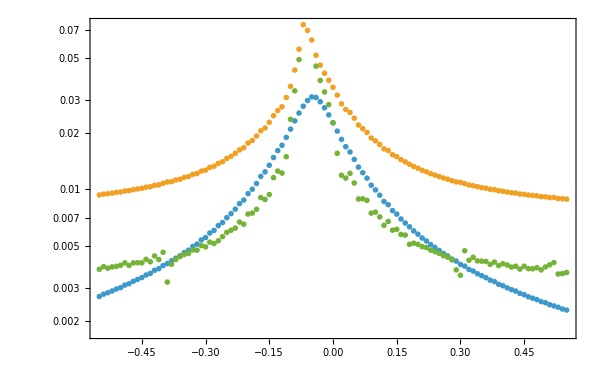

```mathematica
font="Times";
ListLogPlot[{{ΔLIST,Total[KDᵀ]/Nsteps}ᵀ,{ΔLIST,Total[RHPᵀ]/Nsteps}ᵀ,{ΔLIST,Total[LFSᵀ]/Nsteps}ᵀ},
PlotRange->All,
PlotMarkers->{"OpenMarkers",6},PlotLegends->Placed[{Style[MaTeX["\\sum\\mathcal{N}_q",Magnification->2]],Style[MaTeX["\\mathcal{I}_{\\text{RHP}}",Magnification->2]],Style[MaTeX["\\mathcal{I}_{\\text{LFS}}",Magnification->2]]},{0.85,0.75}],Frame->True,FrameStyle->Directive[FontFamily->font,24,Black],Axes->False,ImageSize->600,FrameLabel->{Style[MaTeX["\Delta \omega",Magnification->2]]},LabelStyle->Directive[FontFamily->font,24,Black],PlotTheme->"Detailed"]
```

## Figure 4

Comment: Parameter-scan block for Fig. 4. The code sweeps the interaction anisotropy gamma and compares how the KDQ, RHP, and LFS diagnostics respond.

## PARAMETERS

Comment: Sets fixed thermal and coupling parameters for the gamma sweep. The interaction anisotropy gamma is varied later inside the Table.

```mathematica
ClearAll[ω,ωs,ωm,ωe,gsm,gme,γ,λ,ττ,βS,βM,βE]
NN=3;
ω=1.;
ωs=ω;
ωm=ω;
ωe=ω;
gsm=ω/5;
gme=ω/5;
ττ=ω/5;
βS=0;
βM=1.;
βE=1.;
λ=0;
```

```mathematica
ρS0=({{1/(1+ⅇ^(βS ωs)), 0}, {0, ⅇ^(βS ωs)/(1+ⅇ^(βS ωs))}});
ρM0=({{1/(1+ⅇ^(βM ωm)), 0}, {0, ⅇ^(βM ωm)/(1+ⅇ^(βM ωm))}});
ρEth=({{1/(1+ⅇ^(βE ωe)), 0}, {0, ⅇ^(βE ωe)/(1+ⅇ^(βE ωe))}});
χE={{0,λ},{λ,0}};
ρE0=ρEth+χE;
```

## COLLISIONS definition, evolution, KDQ,RHP,LFS

Comment: Runs the gamma sweep. For each anisotropy value, the code rebuilds the interaction unitaries, evaluates KDQ, RHP, and LFS diagnostics, and stores the results in res.

```mathematica
NQubits[NN];
Nsteps=1001;
GG1={{{1,0},{0,0}},{{0,0},{1,0}},{{0,1},{0,0}},{{0,0},{0,1}}};
P=id⊗({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})⊗id;

Clear[HS,HM,HSM,HME]
HS=ωs/2 Sz[1];
HM=ωm/2 Sz[2];
HE=ωe/2 Sz[3];

HSM[γ_]:=gsm/2((1-γ)Sx[1].Sx[2]+(1+γ)Sy[1].Sy[2]+Sz[1].Sz[2]);
HME[γ_]:=gme/2((1-γ)Sx[2].Sx[3]+(1+γ)Sy[2].Sy[3]+Sz[2].Sz[3]);
```

```mathematica
γLIST=Range[-1,1,0.02];
```

```mathematica
res=Table[
USM=MatrixExp[-ⅈ (HS+HM+HE+HSM[γ]) ττ];
USMc=MatrixExp[ⅈ (HS+HM+HE+HSM[γ]) ττ];
UME=MatrixExp[-ⅈ (HS+HM+HE+HME[0]) ττ];
UMEc=MatrixExp[ⅈ (HS+HM+HE+HME[0]) ττ];
ΦSME[σ_]:=(UME.USM.(PartialTrace[σ,{2,2,2},{3}]⊗ρE0).USMc.UMEc);
ρSME={ρS0⊗ρM0⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
ρSM=Chop@PartialTrace[#,{2,2,2},{3}]&/@ρSME;
ρS=Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME;
ρM=Chop@PartialTrace[#,{2,2,2},{1,3}]&/@ρSME;
ρE=Chop@PartialTrace[#,{2,2,2},{1,2}]&/@ρSME;
ΛSelements=Table[
ρSME={op⊗(ρM0)⊗ρE0};
Table[ρSME=Append[ρSME,ΦSME[ρSME[[-1]]]],{n,1,Nsteps}];
Chop@PartialTrace[#,{2,2,2},{2,3}]&/@ρSME
,{op,GG1}];
LS=Chop@Table[Tr[GG1[[k]].#]&/@(ΛSelements[[j]]),{k,1,4},{j,1,4}];
LS=Transpose[LS,1<->3];
LS=Transpose[LS,2<->3];
iLS=PseudoInverse[#]&/@LS;
LStl=Chop@Table[LS[[n+1]].iLS[[n]],{n,1,Nsteps-1}];
a=LStl[[1;;,1,1]];
b=LStl[[1;;,1,4]];
c=LStl[[1;;,2,2]];
d=LStl[[1;;,2,3]];

choi=Chop@(1/2 Sum[(v1⊙v2)⊗Partition[#.Flatten[(v1⊙v2)],2],{v1,{m,p}},{v2,{m,p}}])&/@LStl;
LSF2=Table[MutualInformation[Partition[P.(Id[4]⊗LStl[[n]]).P.Flatten[choi[[n]]],4]]-MutualInformation[choi[[n]]],{n,1,Nsteps-1}];{Chop[-1+ρS[[All;;-3,1,1]] (Abs[1-a]+Abs[a])+ρS[[All;;-3,2,2]] (Abs[1-b]+Abs[b])],-1+1/2 Abs[1-a]+Abs[b]/2+1/4 Abs[1+a-b-√((-1+a+b)^2+4 Abs[c]^2)]+1/4 Abs[1+a-b+√((-1+a+b)^2+4 Abs[c]^2)],LSF2+(Sign[LSF2]-1)/2 LSF2},{γ,γLIST}];
```

```mathematica
γ
```

-0.76

```mathematica
{KD,RHP,LFS}={res[[All,1]],res[[All,2]],res[[All,3]]};
```

## PLOTS

Comment: Assembles and plots the gamma-dependent arrays, with gammaLIST providing the horizontal parameter axis.

```mathematica
<<"MaTeX`"
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

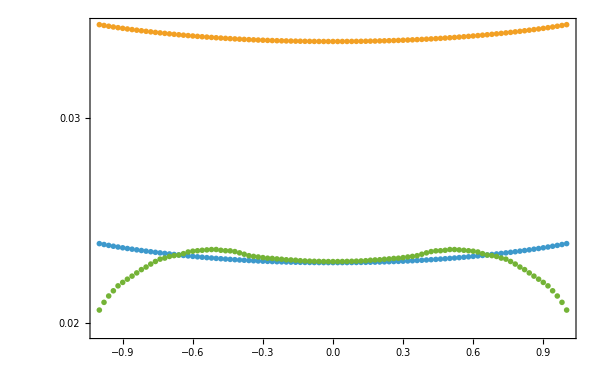

```mathematica
font="Times";
ListLogPlot[{{γLIST,Total[KDᵀ]/Nsteps}ᵀ,{γLIST,Total[RHPᵀ]/Nsteps}ᵀ,{γLIST,Total[LFSᵀ]/Nsteps}ᵀ},
PlotRange->All,
PlotMarkers->{"OpenMarkers",6},PlotLegends->Placed[{Style[MaTeX["\\sum\\mathcal{N}_q",Magnification->2.5]],Style[MaTeX["\\mathcal{I}_{\\text{RHP}}",Magnification->2.5]],Style[MaTeX["\\mathcal{I}_{\\text{LFS}}",Magnification->2.5]]},{0.5,0.60}],Frame->True,FrameStyle->Directive[FontFamily->font,24,Black],Axes->False,ImageSize->600,FrameLabel->{Style[MaTeX["\gamma",Magnification->2.5]]},LabelStyle->Directive[FontFamily->font,24,Black],PlotTheme->"Detailed"]
```